```mathematica
f[y_,Ex_,lb_,n_]:=(y/Ex)^2*Exp[-y]*(y+lb*Ex)^n/Factorial[n]/Sum[(lb*Ex)^k/Factorial[k],{k,0,n}]
```

```mathematica
? f
```

Global`f

f[y_,Ex_,lb_,n_]:=(y Exp[-y] (y+lb Ex)^n)/((Ex^2 n!) ∑_(k=0)^n (lb Ex)^k/(k!))

```mathematica
f1[Ex_,lb_,n_]:=Integrate[f[y,Ex,lb,n], {y,0,Infinity}, Assumptions->n ∈Integers && n>0 ]
```

```mathematica
N[f1[10, 10, 1000]]
```

9.01

```mathematica
Integrate[f[y,Ex,lb,n], {y,0,Infinity}, Assumptions->n ∈Integers && n>0  && {Ex, lb}∈Reals && {Ex,lb}>0]
```

(ⅇ^(-Ex lb) lb^2 (-Ex lb+n+ⅇ^(Ex lb) (Ex^2 lb^2-2 Ex lb (1+n)+(1+n) (2+n)) ExpIntegralE[-2-n,Ex lb]))/((1+n) (2+n) ExpIntegralE[-n,Ex lb])

```mathematica
p[a_,b_,n_]:=(a+b)^n*Exp[-(a+b(1+1/b0))]
```

```mathematica
pa=Integrate[p[a,b,n],{b,0,Infinity},{a,0,Infinity}, Assumptions->n∈ Integers && n>0 && {a,b}∈Reals && {a,b}>0 && b0>0]
```

-(b0 (-1+b0 (-1+(b0/(1+b0))^n)) Gamma[1+n])/(1+b0)

```mathematica
Integrate[p[a,b,n],{b,0,Infinity},Assumptions->n∈ Integers && n>0 && {a,b}∈Reals && {a,b}>0 && b0>0]
```

a^(1+n) ⅇ^(a/b0) ExpIntegralE[-n,a (1+1/b0)]

```mathematica
pf [a_,b_,n_]:=Exp[-a]*(a+b)^n/Factorial[n]/Sum[b^k/Factorial[k],{k,0,n}]
```

```mathematica
pfprior[a_,b0_,n_]:=(b0/(b0+1))^n*Exp[-a]/(1+b0*(1-(b0/(b0+1))^n))*Sum[(a*(1+1/b0))^k/Factorial[k],{k,0,n}]
```

```mathematica
Integrate[pf[a,b0,n],{a,0,Infinity},Assumptions->n∈ Integers && n>0 && {a,b0}∈Reals && {a,b0}>0 ]
```

((b0/(1+b0))^n (-b0+(1+1/b0)^n (1+b0)))/(1+b0-b0 (b0/(1+b0))^n)

```mathematica
Integrate[a*pf[a,b0,n],{a,0,Infinity},Assumptions->n∈ Integers && n>0 && {a,b0}∈Reals && {a,b0}>0 ]
```

((b0/(1+b0))^n (b0^2-(1+1/b0)^n (1+b0) (-1+b0-n)))/(1+b0-b0 (b0/(1+b0))^n)

```mathematica
Integrate[a^2*pf[a,b0,n],{a,0,Infinity},Assumptions->n∈ Integers && n>0 && {a,b0}∈Reals && {a,b0}>0 ]
```

((b0/(1+b0))^n (-2 b0^3+(1+1/b0)^n (1+b0) (2 b0^2-2 b0 (1+n)+(1+n) (2+n))))/(1+b0-b0 (b0/(1+b0))^n)

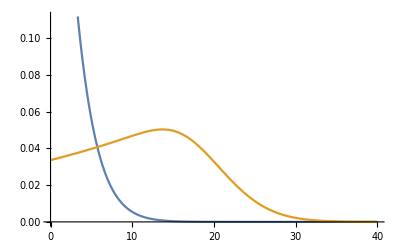

```mathematica
Plot[{pf[x,30,20], pfprior[x,30,20]}, {x,0,40}]
```

```mathematica
NIntegrate[x*pfprior[x,10000,20],{x,0,Infinity}]
```

11.0037